```mathematica
thisdir=NotebookDirectory[]
```

/Users/Emily/Documents/Columbia/planetary_linguistics/multiPlanetDist_fixedForecaster/

```mathematica
<<ErrorBarPlots`
```

```mathematica
files=FileNames[StringJoin[thisdir,"/fakesResults/fitZipftofakeZipf*10k.dat"]];j=0;Label[jloop];j=j+1;temp=Import[files[[j]],"Table"];temp=temp[[2;;All]];row=0;Label[rloop];row=row+1;tempy=StringSplit[StringDelete[StringDelete[ToString[temp[[row]]],"{"],"}"],","];col=0;Label[cloop];col=col+1;dummy=ToExpression[StringSplit[tempy[[col]],"e"]];Subscript[element, col]=dummy[[1]]*10^(dummy[[2]]);If[col<Length[tempy],Goto[cloop]];Subscript[thisrow, row]=Table[Subscript[element, c],{c,1,Length[tempy]}];If[row<Length[temp],Goto[rloop]];Subscript[post, j]=Table[Subscript[thisrow, r],{r,1,Length[temp]}];Subscript[quantiles, j]=Table[{{j-0.0,Median[Subscript[post, j][[All,i]]]},ErrorBar[{Quantile[Subscript[post, j][[All,i]],0.5-0.5Erf[1/√2]]-Median[Subscript[post, j][[All,i]]],Quantile[Subscript[post, j][[All,i]],0.5+0.5Erf[1/√2]]-Median[Subscript[post, j][[All,i]]]}]},{i,1,Last[Dimensions[Subscript[post, j]]]-1}];If[j<Length[files],Goto[jloop]];
```

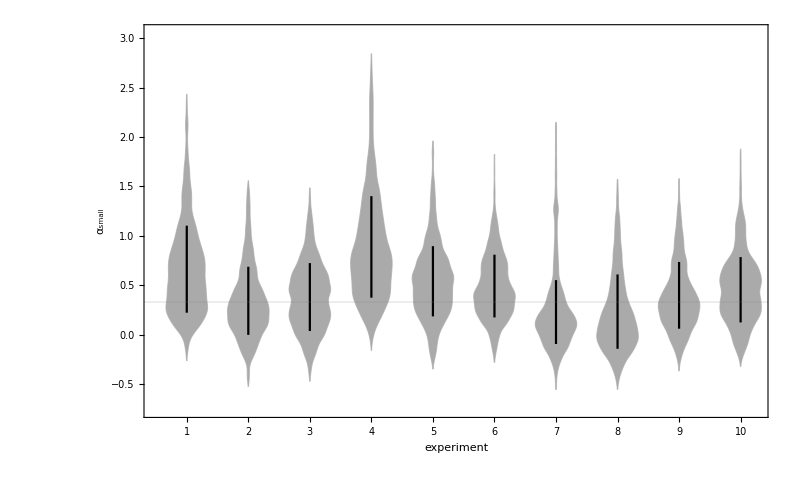

```mathematica
Show[DistributionChart[Table[Subscript[post, i][[All,1]],{i,1,10}],ChartStyle->Lighter[Gray], ChartElementFunction->"SmoothDensity",ChartBaseStyle->EdgeForm[Thick],ImageSize->{800,550},BaseStyle->{FontFamily->"CMu Serif",FontSize->28},Frame->True,FrameLabel->{"experiment","α_small"},ChartLabels->Range[10],PlotRange->{{0.5,10.25},All},GridLines->{{},{0.33}}],ErrorListPlot[Table[Subscript[quantiles, j],{j,1,10}][[All,1]],PlotStyle->Black,Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing]
```

```mathematica
k=0;Label[kloop];k=k+1;Subscript[list, k]=Table[Subscript[quantiles, j],{j,1,10}][[All,k]][[All,1]];If[k<Last[Dimensions[Subscript[post, 1]]]-1,Goto[kloop]];
```

```mathematica
names={"α_small","α_big","R_crit [R_♁]","σ_R [R_♁]","β_Zipf","σ_I [°]",};
truth={0.33,5.00,2.50,0.05,1.00,2.00};
```

```mathematica
k=0;Label[kloop];k=k+1;Subscript[plot, k]=Show[DistributionChart[Table[Subscript[post, i][[All,k]],{i,1,10}],ChartStyle->"CandyColors", ChartElementFunction->"HistogramDensity",Method->{"BoxWidth"->"Fixed"},ChartBaseStyle->EdgeForm[Directive[Thin,Lighter[Black]]],AspectRatio->0.3,ImageSize->{800,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->28},Frame->True,FrameLabel->{"experiment",names[[k]]},ChartLabels->Range[10],PlotRange->{{0.5,10.25},All},GridLines->{{},{{truth[[k]],Directive[Black,Thickness[0.002]]}}}],ErrorListPlot[Table[Subscript[quantiles, j],{j,1,10}][[All,k]],PlotStyle->Black,Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing,ListPlot[Subscript[list, k],PlotMarkers->{"●",15},PlotStyle->Black]];If[k<Last[Dimensions[Subscript[post, 1]]]-1,Goto[kloop]];
```

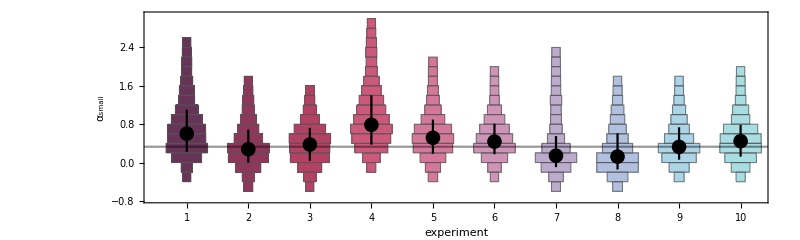

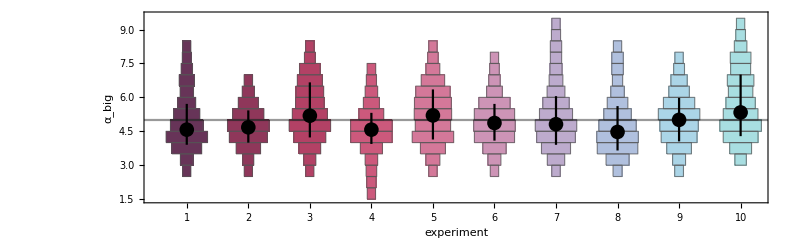

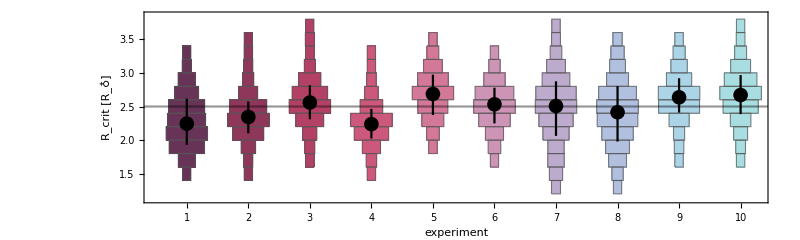

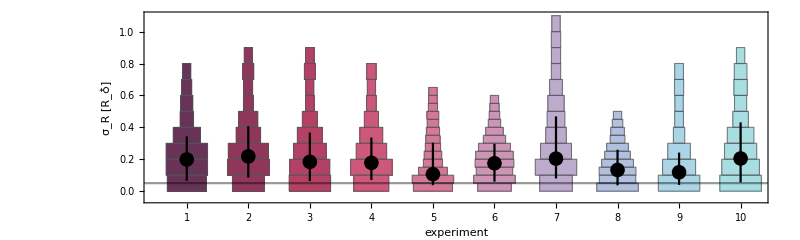

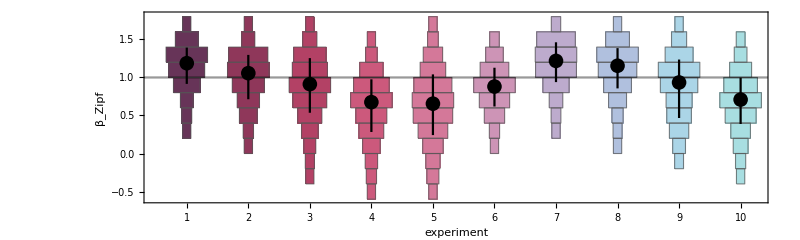

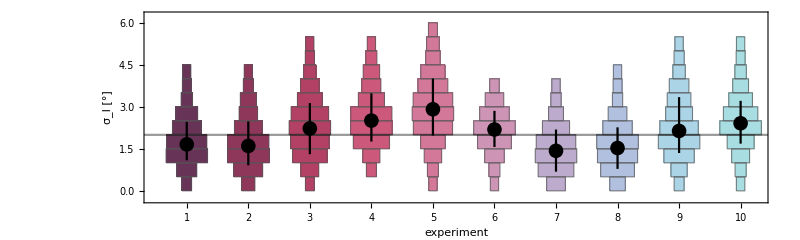

```mathematica
Subscript[plot, 1]
Subscript[plot, 2]
Subscript[plot, 3]
Subscript[plot, 4]
Subscript[plot, 5]
Subscript[plot, 6]
```